```mathematica
$BaseSpacerSize=1;
$BaseObjectSize=1;

$DefaultColorGradient="DeepSeaColors";


(* element, index, level, spacing, object size, agg, color, aggregation *)





ClearAll[LevelSpacerFunction,LevelSizeFunction,LevelColorFunction]
LevelSpacerFunction[level_Integer,levelData_:{}]:=$BaseSpacerSize/;level==0
LevelSpacerFunction[level_Integer,levelData_:{}]:=$BaseSpacerSize /level;
LevelSizeFunction[level_Integer, levelData_:{}]:=$BaseObjectSize ;
LevelColorFunction[level_Integer,levelData_:{},maxDepth_:1]:=ColorData[$DefaultColorGradient][level/maxDepth]
```

```mathematica
SpacingOfElements[
list_List,
level_:1,
spacingFunction_:LevelSpacerFunction,
sizingFunction_:LevelSizeFunction
]:=Map[SpacingOfElements[
#,level,
spacingFunction,
sizingFunction
]&,list]
```

# b3m2a1 approach

```mathematica
ExtractListStructure[list_List]:=
Module[
{i=1},
Reap[
MapIndexed[
If[
!ListQ@#,
Print[#, Length@#2, Last@#2];
Sow[{#,i++,Length@#2}]
]&,
list,
All]
][[2,1]]
];
ClearAll[ExtractListStructure]

$IndexForElement=1
$IndexForFlattenedPosition=2
$IndexForLevel=3
$IndexForLevelPosition=4
$IndexForLastInLevelInstanceQ=5


ExtractListStructure[ll_,atomQ_: Not@*ListQ]:=
Block[
{
i=1,
prev=None
},
Reap[
MapIndexed[
Function[
If[atomQ@#,
If[ListQ@prev,prev[[5]]=False;Sow@prev];
prev={#,i++,Length@#2,Last@#2, None},

If[ListQ@prev,prev[[5]]=True;Sow@prev;prev=None]
];
#
],ll,All
]
][[2,1]]
];

(*element, index, level *)
```

```mathematica
el=ExtractListStructure[{1,{2,2},{3,2}}]
```

{{1,1,1,1,False},{2,2,2,1,False},{2,3,2,2,True},{3,4,2,1,False},{2,5,2,2,True}}

```mathematica
ClearAll[ApplyPositioningFunctions]
ApplyPositioningFunctions[
extracted_List,
spacingFunction_:LevelSpacerFunction,
sizingFunction_:LevelSizeFunction,
coloringFunction_:LevelColorFunction
]:=Module[
{
maxDepth=Max@extracted[[;;,3]],
},
Map[
Join[
#,
{
If[
#[[4]],
(* Last element in current instance of level, needs spacing of previous level *)
spacingFunction[#[[3]]-1, #[[1]]],
spacingFunction[#[[3]], #[[1]]]
],

sizingFunction[#[[3]], #[[1]]],
0,
coloringFunction[#[[3]], #[[1]], maxDepth]
}
]&
, extracted]
]

(* element, index, level, lastElementInLevel, spacing, object size, aggregatedValue, color *)
```

```mathematica
el=ExtractListStructure[{1,{2,{2},2},1}];
apf=ApplyPositioningFunctions[el];
apf//TableForm
```

32

21

10

1 | 1 | 1 | False | 1 | 1 | 0 | RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]
2 | 2 | 2 | False | 1/2 | 1 | 0 | RGBColor[0.26669366666666666, 0.550462, 0.926485]
2 | 3 | 3 | True | 1/2 | 1 | 0 | RGBColor[0.772061, 0.92462, 0.998703]
2 | 4 | 2 | True | 1 | 1 | 0 | RGBColor[0.26669366666666666, 0.550462, 0.926485]
1 | 5 | 1 | True | 1 | 1 | 0 | RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]

```mathematica
ClearAll[PositionPlus]
(*PositionPlus[a_,b_]:=Join[b[[;;-3]],{Total[a[[4;;6]]]}, {b[[-1]]}]*)
PositionPlus[a_,b_]:=Join[
b[[;;-3]],

{
Total[a[[5;;7]]]
}

,
{
b[[-1]]
}
]
(*AggregateTranslation[a_,b_]:=
Join[
b[[;;-3]], (* element, index, level, spacing, size *)

If[
a[[4]]==b[[4]],
{Total[a[[4;;6]]]}

],

, {b[[-1]]} (* color *)
]*)
```

```mathematica
flpp=FoldList[PositionPlus,apf]
```

1 1/2

1/2 1/3

{{1,1,1,False,1,1,0,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]},{2,2,2,False,1/2,1,3/2,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{2,3,3,True,1/3,1,17/6,RGBColor[0.772061, 0.92462, 0.998703]},{2,4,2,True,1,1,25/6,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{1,5,1,True,1,1,37/6,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]}}

```mathematica
ClearAll[ToRect]
ToRect[flpp_]:=
Map[
With[
{
color=#[[-1]],
size = #[[6]],
data=#[[1]],
aggregatedSpacer=#[[-2]]
},
Translate[{color,Rectangle[{0,0},{size,data}]},{aggregatedSpacer,0}]
]&,
flpp
]
```

{{1,1,1,False},{2,2,2,False},{2,3,3,False},{2,4,3,True},{2,5,2,True},{1,6,1,True}}

{{1,1,1,False,1,1,0,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]},{2,2,2,False,1/2,1,0,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{2,3,3,False,1/3,1,0,RGBColor[0.772061, 0.92462, 0.998703]},{2,4,3,True,1/2,1,0,RGBColor[0.772061, 0.92462, 0.998703]},{2,5,2,True,1,1,0,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{1,6,1,True,1,1,0,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]}}

{{1,1,1,False,1,1,0,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]},{2,2,2,False,1/2,1,2,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{2,3,3,False,1/3,1,7/2,RGBColor[0.772061, 0.92462, 0.998703]},{2,4,3,True,1/2,1,29/6,RGBColor[0.772061, 0.92462, 0.998703]},{2,5,2,True,1,1,19/3,RGBColor[0.26669366666666666, 0.550462, 0.926485]},{1,6,1,True,1,1,25/3,RGBColor[0.28235299999999997, 0.1497248, 0.6790623333333333]}}

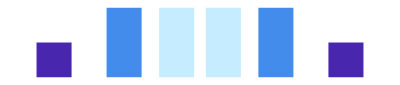

```mathematica
el=ExtractListStructure[{1,{2,{2,2},2},1}]
apf=ApplyPositioningFunctions[el]
flpp=FoldList[PositionPlus,apf]
ToRect[flpp]//Graphics
```

```mathematica
N/@Differences@flpp[[;;,7]]
```

{2.,1.5,2.,2.}